```mathematica
figNo=1;
captionStyle={FontFamily-> "Book Antiqua", FontSize->14};
$Line=0;
```

# Chapter 54 | Supporting Notebook Curve Fitting revision 4

## Installing and Checking the IP Package

This installs the IP package, lists and counts the defined functions in IP.m.

```mathematica
Needs["IP`"]
functionListing["IP`"]
functionCount["IP`"]
```

## Introduction

In this Supporting Notebook for Chapter 54, Curve Fitting, we provide working Mathematica code reflecting accurately as possible the code presented by David Blower in the text of his Chapter 54, Volume IV.

As discussed elsewhere, this SN and it’s companion Supporting Notebooks will make extensive use of the functions defined in the IP package, which must be loaded first before the code in each Notebook will execute as intended. If the following Needs[] statements executes properly, the full Notebook should execute without error in a running time of around 60 seconds.

## 54.1 Introduction

This is the complete Introduction:

$Line=$Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 103.", 120  ],figNo++], captionStyle ],600 ]

## 54.2 Series Expansion of an Arbitrary Function

This section introduces the general mathematical concept of a series expansion.

$Line=$Line-1;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 103-104.", 120  ],figNo++], captionStyle ],600 ]

This section concludes:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 105.", 120  ],figNo++], captionStyle ],600 ]

## 54.3 Bishop’s Polynomial Curve Fit

$Line=$Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 105.", 120  ],figNo++], captionStyle ],600 ]

We have interpreted “Following Bishop, take this function …” to mean that Bishop’s Figure 1.2 is the inspiration but not the precise model for DB’s Figure 54.1.
Here is Bishop’s Figure 1.2, …

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Christopher M. Bishop's
''Pattern Recognition and Machine Learning'', page 4.", 120  ],figNo++], captionStyle ],600 ]

… showing what is clearly a plot of Sin[2 π x], 0 ≤x ≤ 1, with some “training data” (Bishop’s term), i.e., 10 data points generated by (in Mathematica notation) something like…

Table[ {x, Sin[2 π x] + RandomVariate[ NormalDistribution[0, 0.25] ]}, {x, 0, 1, 1/9} ]

The choice of σ = 0.25 in this code gives “simulated” Bishop data having similar statistics, for example:

$Line=$Line-4;
blueCircle = Graphics[ {Blue, Circle[{0,0}, 0.025//Scaled]}   ];
Show[ {Plot[Sin[2 π x], {x, 0, 1},PlotStyle->{Green} ],ListPlot[{{0,-0.323844},{1/9,0.166339},{2/9,1.01744},{1/3,1.06207},{4/9,0.465861},{5/9,-0.854933},{2/3,-0.911644},{7/9,-1.10192},{8/9,-0.904036},{1,-0.166223}}, PlotMarkers->{blueCircle}]}, Frame->True,Axes->False, PlotRange->{{-0.05,1.05},{-1.25,+1.25}}, ImageSize->475 ];
Labeled[ %, Style[ StringForm[captionNeatFigured[ "Simulated ''Bishop data'' having
the same error standard deviation.", 140  ],figNo++], captionStyle ] ]//Print

Here is DB’s Figure 54.1:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 106.", 120  ],figNo++], captionStyle ],600 ]

(Although the noisy data in DB’s Figure 54.1 was not directly available to us, hand-digitizing the original Figure allowed us to re-fit a cubic polynomial, giving the model
0.498505+4.18007 x-13.0395 x^2+9.01344 x^3, which compares well with DB’s model,
0.500662+4.15496 x-12.9961 x^2+8.99089 x^3.

DB’s sine function is clearly different from the pure Sin[2πx] function used by Bishop.

Even when you have Bishop’s curvefitting.txt file, there is still some work to do to turn it into a Mathematica coordinate list.

```mathematica
Import[ NotebookDirectory[]<>"Bishop's data | curvefitting.txt" ];
(* replace various newlines *)
StringReplace[ %,
{
"\n\n"->",",
"\n"->",",
" "->","
}];
(* wrap the resulting string with { and } *)
"{"<>%<>"}";
(* convert to an expression, suppressing the error message due to the final "," *)
ToExpression[%]//Quiet;
(* drop the final "," *)
Drop[ %,-1 ];
(* paretion into {x,y} coordinates *)
Partition[ %, 2 ]
(* check the dimensions of the list *)
Dimensions[%]
```

However obtained, we assign these coordinates to bishopSinData:

```mathematica
bishopSinData = {{0.,0.349486},{0.111111,0.830839},{0.222222,1.007332},{0.333333,0.971507},{0.444444,0.133066},{0.555556,0.166823},{0.666667,-0.848307},{0.777778,-0.445686},{0.888889,-0.563567},{1.,0.261502}};
bishopSinData = Transpose[ {Rationalize[bishopSinData, 0.0001]⟦All,1⟧,bishopSinData⟦All,2⟧} ]
```

$Line=$Line-1;codeInTextCell[ "Mimicking his plotting styles, Figure", figNo, "very closely reproduces Bishop's Figure 1.2." ]

$Line=$Line-4;
blueCircle = Graphics[ {Blue, Circle[{0,0}, 0.025//Scaled]}   ];
gr=Show[ {Plot[Sin[2 π x], {x, 0, 1},PlotStyle->{Green} ],ListPlot[bishopSinData, PlotMarkers->{blueCircle}]}, Frame->True,Axes->False, PlotRange->{{-0.05,1.05},{-1.25,+1.25}}, ImageSize->475 ];
Labeled[ gr, Style[ StringForm[captionNeatFigured[ "Regenerated Figure 1.2 from Christopher M. Bishop's
''Pattern Recognition and Machine Learning'', page 4.", 140  ],figNo++], captionStyle ] ]//Print

According to Mathematica’s Fit[] function, the amplitude of the sine function fitted to the Bishop data without intercept is 0.864824:

```mathematica
bishopSinDataFit = Fit[bishopSinData, {Sin[2 π x]}, x]
```

Allowing for a non-zero intercept, the amplitude is the same:

```mathematica
bishopSinDataFit = Fit[bishopSinData, {1,Sin[2 π x]}, x]
```

LinearModelFit[] allows for extraction of additional information about the fitting.
There is no statistical evidence for either an intercept or a slope.

```mathematica
LinearModelFit[bishopSinData, {1,x, Sin[2 π x]}, x]
%[ {"ParameterTable"} ]
```

Mathematica’s NonlinearModelFit[] function gives the same fitted model of the form a+b*Sin[2πx]:

```mathematica
NonlinearModelFit[bishopSinData,a + b Sin[2 π x],{a,b},x]
```

Dispensing with an intercept and slope, but allowing for a frequency-related parameter, NonlinearModelFit[] gives a similar estimate for the amplitude, and quite accurate estimate of the frequency, given only 10 data points.

```mathematica
NonlinearModelFit[bishopSinData,a Sin[b π x],{a,b},x]
%[ "ParameterTable" ]
%%[ "ParameterConfidenceIntervalTable" ]
```

## 54.4 Pure Probabilistic Analysis

$Line=$Line-2;
codeInTextCell[ "Figure", figNo, "below shows the complete Section." ]

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 106.", 120  ],figNo++], captionStyle ],600 ]

DB’s detailed approach to applying an ANN to the data in his Figure 54.2 is set out in his 
Exercise 54.9.5: Generate some synthetic data from a known function, discussed below.
We note that he does not discretize the dependent y variable as described here, but generates a dataset of the form …

{-4.0 -> 0.011835, -3.6 -> 0.0598361, …, 4. -> 0.121519}

… as shown on page 118.

## 54.5 Connections to the Literature

DB’s discussion in this Section …

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 107.", 120  ],figNo++], captionStyle ],600 ]

… leads to a polemic in his somewhat pointedly titled Exercise 54.9.2: Solve Bishop's Exercise 1.9 the correct way on the whole topic of the meaning of a correct understanding of what a probability is, what randomness is, what’s wrong with frequentism, and the high importance of correct notation.
Exercise 54.9.2: Solve Bishop’s Exercise 1.9 the correct way starts: “Here is the correct solution approached as a canonical inference. ”

One of us (BJS) has long fancied—but can’t find the reference—that Einstein once said that in solving a mathematical problem, a good notation is half the battle. DB shares with Jaynes and Bretthorst the consistent use of the correct notation for probabilities (introduced by Harold Jeffreys, the dedicatee of Probability Theory: the Logic of Science) that makes such operations as marginalisation straightforward and transparent.

Most of “Connections to the Literature” is concerned with criticism of the approach taken by Christopher Bishop in setting out and discussing a problem given in Bishop’s 2006 book Pattern Recognition and Machine Learning. This is an urn problem, of the type much used to introduce Bayes’ Theorem and its use in calculating so-called inverse probabilities: given that an apple has been randomly drawn from one of two randomly selected boxes containing various (known) numbers of apples and oranges, from which box was the apple selected?

Bishop presents a straightforward analysis, using Bayes’ Theorem with probabilities derived directly from the ratios of the counts of apples and oranges in the two boxes. DB criticises this approach, presented in Exercise 54.9.1, “Solve Bishop’s Exercise 1.9” (see below), and in Exercise 54.9.2, “Solve Bishop’s Exercise 1.9 the correct way”, and obtains a different value for, in an obvious notation, the posterior probability Pr(box1 | apple) than is given via Bayes’ Theorem (see below).

Note that Bishop’s Exercise 1.9—the focus of Exercise 54.9.1 and 54.9.2—is another “fruit-in-boxes” problem posed in his’s 1993 book Neural Networks for Pattern Recognition

This is a representative and typical extract from page 109:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 109.", 120  ],figNo++], captionStyle ],600 ]

One of us (BJS) has simulated Bishop’s Exercise 1.9, obtaining results that are consistent with Bishop’s analysis with a “predictor” that infers the selected box given the selected fruit on the basis of Bishop’s posterior probabilities. This Bishop’s Exercise 1.9.nb Notebook also contains a full discussion of the two closely related Bishop problems one in his 1993 book, and the other in his 2006 book, and a critique of DB’s use of these problems.

$Line=$Line-1;Button["Bishop's Exercise 1.9.nb", NotebookOpen[ NotebookDirectory[]<>"Bishop's Exercise 1.9.nb" ],Appearance->{ "Pressed"}]//Print

## 54.6 Solved Exercises for Chapter Fifty Four

### Exercise 54.9.1: Solve Bishop’s Exercise 1.9.

The discussion of Bishop’s solution starts:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 112.", 120  ],figNo++], captionStyle ],600 ]

DB concludes:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 112.", 120  ],figNo++], captionStyle ],600 ]

### Exercise 54.9.2: Solve Bishop’s Exercise 1.9 the correct way.

DB starts with:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 113.", 120  ],figNo++], captionStyle ],600 ]

DB’s analysis of Exercise 1.9 could be called the “joint statements in a state space” approach, and poses Bishop’s question accordingly in the same language:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 113.", 120  ],figNo++], captionStyle ],600 ]

Taking the view that we (yet?) have no data counts on which to base calculations of joint statements via Laplace’s Rule of Succession, DB derives two such probabilities:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 114.", 120  ],figNo++], captionStyle ],600 ]

These two probabilities are, again in an obvious notation, Pr(box1 ∧ apple) and Pr(box2 ∧ apple).
Since as yet have no data counts, these are both equal to

(0 + 1)/(0 + 4)=1/4

DB then proceeds to his final calculation:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 114.", 120  ],figNo++], captionStyle ],600 ]

Here DB is saying that

Pr(box1 | apple) =(Pr(box1 ∧ apple))/(Pr(apple))

= (Pr(box1 ∧ apple))/(Pr(box1 ∧ apple)+Pr(box2 ∧ apple))

With all the joint statement having probability 1/4.

At this stage many a reader might feel at a loss to explain this “data free” result, and be wondering why the stated counts of apples and oranges did not play any rôle in this calculation.

DB is nothing if not persistent and consistent in his advocacy of the “correct” approach:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 114-5.", 120  ],figNo++], captionStyle ],600 ]

### Exercise 54.9.3: How are these probabilities affected by the presence of data?

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Christopher M. Bishop's
''Neural Networks for Pattern Recognition'', page 32.", 120  ],figNo++], captionStyle ],600 ]

Since DB is using probabilities via Laplace’s Rule of Succession, he needs some data to arrive at “data-based” probabilities such as Pr(box1 | apple).

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 115-6.", 120  ],figNo++], captionStyle ],600 ]

DB’s final calculated value is NOT Pr(box1 | apple). The key words in the correct interpretation of DB’s probability are “next trial”.

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 116.", 120  ],figNo++], captionStyle ],600 ]

We comment that, in pointing out the slightly different results 81/182 vs. 4/9, i.e., 0.445055 vs. 0.44444, DB is implicitly pointing out that he and Bishop have solved two slightly different problems.

### Exercise 54.9.4: Highlight the step within the detailed derivation of the posterior predictive formula where the averaging with respect to the posterior probability over model space occurs.

This problem involves a page or so of straightforward but careful derivation of the required formula:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 118.", 120  ],figNo++], captionStyle ],600 ]

### Exercise 54.9.5: Generate some synthetic data from a known function.

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 118.", 120  ],figNo++], captionStyle ],600 ]

```mathematica
data = Table[x -> Exp[-x^2] +
RandomVariate[NormalDistribution[0, .20]], {x, -4, 4, .4}]
```

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 118.", 120  ],figNo++], captionStyle ],600 ]

```mathematica
Length[ data ]
```

```mathematica
Sort[ Values[data], Greater ]
```

$Line=$Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 106.", 120  ],figNo++], captionStyle ],600 ]

$Line=$Line-1;codeInTextCell[ "Since in a later Exercise we want to explore the use of an ANN to fit models to DB's data, we have hand-digitized the data points in Figure 54.2, and re-plotted them in Figure", figNo, "below." ]

In constructing the following Figure, the coordinates are assigned for later use to the variable noisyGaussianDataDB.

$Line=$Line-3;
Show[
 {
ListPlot[ noisyGaussianDataDB={{-4.,0.0049914},{-3.6,-0.0703791},{-3.2,-0.161699},{-2.8,-0.00389006},{-2.4,-0.194879},{-2.,-0.219929},{-1.6,-0.0311534},{-1.2,0.35811},{-0.8,0.391916},{-0.4,0.828859},{0.,1.07147},{0.4,1.05536},{0.8,0.573861},{1.2,0.311208},{1.6,0.11068},{2.,0.119198},{2.4,0.328424},{2.8,0.276478},{3.2,-0.131079},{3.6,-0.529193},{4.,0.113991}}, PlotMarkers→,
GridLines→{Table[  k, {k, -4,+4, 0.8}],Table[  k, {k, -1,+1, 0.2}]} ],
Plot[ ⅇ^(-x^2), {x, -4,4}, PlotStyle→{Thickness[0.0025],Dashed,Blue},Axes->True ]
},
PlotRange→{{-4,4}, {-1,1}},Axes->True, ImageSize->450, Frame→True,FrameLabel->{"x","y"}, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]).",figNo++], captionStyle] ]//Print

### Exercise 54.9.6: Construct a histogram of the synthetic data in order to help fill in the contingency table.

This is the complete Solution to Exercise 54.9.6.

$Line=$Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 119.", 120  ],figNo++], captionStyle ],600 ]

Noting that our data is not DB’s data, the indicated code—along with some cosmetic details—gives a similar plot (reproducing DB’s plot caption):

$Line=$Line-3;
Histogram[Values[data], {-1.1, 1.1, .2}, Frame->True, FrameLabel->{"y","Count"}];
Labeled[ %, Style[ StringForm["Figure `1`. Histogram of data for curve fit of function ⅇ^(-SuperscriptBox[x, 2]) + noise.",figNo++], captionStyle] ]//Print

Using instead our digitised data, noisyGaussianDataDB, we can essentially reproduce DB’s Figure 54.3.

$Line=$Line-3;
Histogram[ noisyGaussianDataDB⟦All, 2⟧, {-1.1, 1.1, .2}, Frame->True, FrameLabel->{"y","Count"}];
Labeled[ %, Style[ StringForm["Figure `1`. Histogram of data for curve fit of function ⅇ^(-SuperscriptBox[x, 2]) + noise.",figNo++], captionStyle] ]//Print

### Exercise 54.9.7: How did Mathematica construct the plot for the curve fitting discussion?

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 119.", 120  ],figNo++], captionStyle ],600 ]

Because of the way data was constructed, a slight adjustment is necessary:

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 120.", 120  ],figNo++], captionStyle ],600 ]

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 120.", 120  ],figNo++], captionStyle ],600 ]

Since the coordinates in datapoints were freshly generated above, a ListPlot[] of them will not give a plot that looks like DB’s Figure 54.2.

dataplot = ListPlot[datapoints,
  PlotStyle -> Gray, PlotRange -> {{-4.1, 4.1}, {-1.2, 1.2}},
  Frame -> True, FrameLabel -> {x, y}]

Substituting our list noisyGaussianDataDB for datapoints gives the intended plot:

dataplot = ListPlot[noisyGaussianDataDB,
  PlotStyle -> Gray, PlotRange -> {{-4.1, 4.1}, {-1.2, 1.2}},
  Frame -> True, FrameLabel -> {x, y}]

$Line=$Line-3;
dataplot=ListPlot[noisyGaussianDataDB,
PlotStyle → Gray, PlotRange → {{-4.1, 4.1}, {-1.2, 1.2}},
Frame → True, FrameLabel → {x, y}];
Labeled[ %, Style[ StringForm["Figure `1`. The intended output from the
ListPlot[] code in Figure `2` above.",figNo++, figNo-2], captionStyle] ]//Print

### Exercise 54.9.8: Set up the network architecture so that the resulting network will “overfit” a set of data points.

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 120-1.", 120  ],figNo++], captionStyle ],600 ]

```mathematica
curvefit = NetChain[{LinearLayer[100], ElementwiseLayer[Tanh],
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1]},
				"Input" -> "Scalar", "Output" -> "Scalar"]
```

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 121.", 120  ],figNo++], captionStyle ],600 ]

Recalling that DB generated data as list of Rules …

data = Table[x -> Exp[-x^2] +
    RandomVariate[NormalDistribution[0, .20]], {x, -4, 4, .4}]

… we need to convert our coordinate list noisyGaussianDataDB to a list of Rules. Thus can be done transparently via …

```mathematica
Map[ (s↦s⟦1⟧->s⟦2⟧), noisyGaussianDataDB ]
```

The training step is not …

curvetrained = NetTrain[curvefit, data]

… but …

```mathematica
(* ⌚ ~22 seconds *)
curvetrained = NetTrain[curvefit, Map[ (s↦s⟦1⟧->s⟦2⟧), noisyGaussianDataDB ]]
```

### Exercise 54.9.9: Write some Mathematica code in order to illustrate what the training has accomplished.

The Notebook accessible via this button presents analyses of the DB noisy Gaussian data involving ANNs and polynomial models fitted to this data. The effects of different starting random number seeds on the ANN-derived fitted function are explored, and three fitting criteria are investigated and compared.

$Line=$Line-1;Button["DB's Noisy Gaussian Data--Digitising & Modeling | Thu01Dec2022.nb", NotebookOpen[ NotebookDirectory[]<>"DB's Noisy Gaussian Data--Digitising & Modeling | Thu01Dec2022.nb" ],Appearance->{ "Pressed"}]//Print

$Line=$Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, page 121.", 120  ],figNo++], captionStyle ],600 ]

The plotting code is straightforward.

$Line=$Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Volume IV, pages 121-2.", 120  ],figNo++], captionStyle ],600 ]

DB’s code is:

Show[dataplot,
 Plot[ curvetrained[x], {x, -4, 4}],
 Plot[ Exp[-x^2], {x, -4, 4}, PlotStyle -> Dashed]
 ]

With a few cosmetic adjustments (e.g., GridLines[]), DB’s code gives a very similar plot, noting again that our freshly computed fitting function curvetrained[] is not DB’s original fitting function, so the behaviour of our curvetrained[] differs in detail—but not in general appearance and quality of fit—from DB’s fitting function.

$Line=$Line-3;
Show[{dataplot,
Plot[ curvetrained[x],{x, -4, 4}],
Plot[ Exp[-x^2],{x, -4, 4}, PlotStyle → Dashed]},
GridLines→{Table[  k, {k, -4,+4, 0.8}],Table[  k, {k, -1,+1, 0.2}]}
];
Labeled[ %, Style[ StringForm["Figure `1`. A reproduction of DB's Figure 54.4.",figNo++, figNo-2], captionStyle] ]//Print

### Further Analyses - 1

We show the quality of fit of 
(i) a Gaussian function of the form a ⅇ^(-b x^2), and;
(ii) a series of polynomials of degree 4 through to degree 8.

```mathematica
nlmf= NonlinearModelFit[noisyGaussianDataDB,a ⅇ^(-b x^2),{a,b},x]
```

nlmf//Normal
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Gaussian: a ⅇ^(-b SuperscriptBox[x, 2]) = `2`",figNo++, nlmf[x]], captionStyle] ]//Print

Even with quite noisy data, the fitted Gaussian function has an SD that is very close to 1:

```mathematica
1/√(b/.nlmf⟦1,2⟧)
```

The degree 4 polynomial already captures the overall shape but does not fit the central bump very well.

nlmf4= NonlinearModelFit[noisyGaussianDataDB,a + b x + c x^2 + d x^3 + e x^4 ,{a,b,c,d,e},x]
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf4[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Polynomial: degree 4.",figNo++, figNo-2], captionStyle] ]//Print

The degree five polynomial hardly does any better.

nlmf5= NonlinearModelFit[noisyGaussianDataDB,a + b x + c x^2 + d x^3 + e x^4 + f x^5,{a,b,c,d,e,f},x]
nlmf5//Normal
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf5[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Polynomial: degree 5.",figNo++, figNo-2], captionStyle] ]//Print

The degree 6 polynomial perhaps strikes the right balance between fitting with a general shape of the data without overfitting, particularly the first seven points, the central three, and the last five.

nlmf6= NonlinearModelFit[noisyGaussianDataDB,a + b x + c x^2 + d x^3 + e x^4 + f x^5+g x^6,{a,b,c,d,e,f,g},x]
nlmf6//Normal
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf6[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Polynomial: degree 6.",figNo++, figNo-2], captionStyle] ]//Print

The degree seven polynomial makes use of the extra odd power by skewing the fitted function in a rather imaginative way concerning the points to the right of zero, but is overfitting the first seven points.

nlmf7= NonlinearModelFit[noisyGaussianDataDB,a + b x + c x^2 + d x^3 + e x^4 + f x^5+g x^6+h x^7,{a,b,c,d,e,f,g,h},x]
nlmf7//Normal
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf7[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Polynomial: degree 7.",figNo++, figNo-2], captionStyle] ]//Print

While fitting the central peak smoothly, the degree 8 polynomial is starting to overfit the first seven points and the last five.

nlmf8= NonlinearModelFit[noisyGaussianDataDB,a + b x + c x^2 + d x^3 + e x^4 + f x^5 + g x^6+h x^7+ j x^8,{a,b,c,d,e,f,g,h,j},x]
nlmf8//Normal
Show[ {ListPlot[noisyGaussianDataDB , PlotStyle->{Gray}],Plot[nlmf8[x], {x, -4,+4} ]}, Frame->True, FrameLabel->{"x","y"} ];
Labeled[ %, Style[ StringForm["Figure `1`. Fitted Polynomial: degree 8.",figNo++, figNo-2], captionStyle] ]//Print

### Further Analyses - 2

Here we present, for further insight into the behaviour of the ANN in the fitting function process, some selected fitted functions obtained by simply varying the random number seed before running code essentially like that reducing the reproduction of DB’s figure 54.4.

As DB suggests, the large number of nodes in the two hidden layers, and thus the 10,000 connections, allows this network to produce a highly nonlinear fitting function and with this power it does a very good job of precisely (over-) fitting the data points.

The following examples are indexed by a fraction which is the size of the largest error made at any of the 21 points by the particular fitting function.

It becomes really apparent that very small maximum errors are associated with rather unlikely fitting functions, knowing as we do that the data is noise surrounding the underlying Gaussian function.

Most of these fitted functions use their non-linear capability to fit the noise represented by the first seven points. The fitting function below indexed by 1/11 could be considered the best of the bunch since it puts a fairly smooth curve through the first seven points and avoids the fairly peculiar double bump at the origin which most of other the fitted functions display.

One lesson from all this could be that the number of nodes in the hidden layers of the ANN could be vastly reduced, avoiding the over fitting problem while still retaining enough flexibility to capture the general shape of this noisy Gaussian data.This is an obvious avenue of further experimentation.

1/40

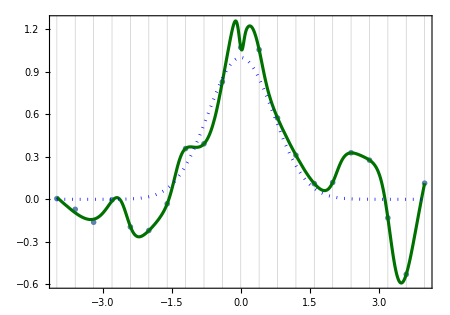
-Graphics-Figure 22. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1/55

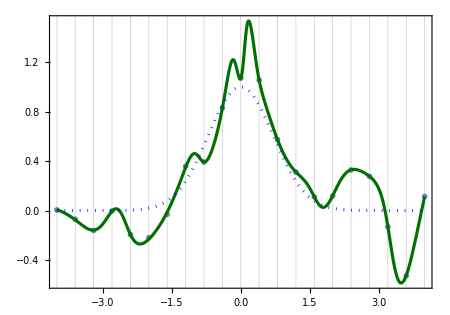
-Graphics-Figure 45. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1/57

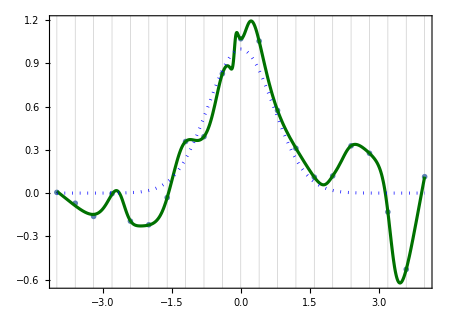
-Graphics-Figure 46. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1.78

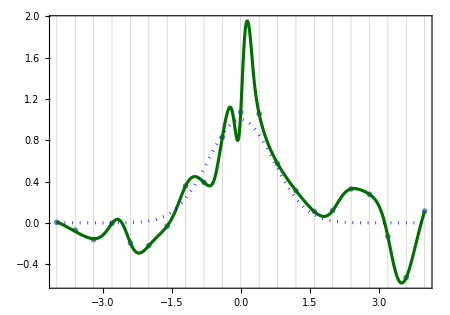
-Graphics-Figure 50. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1/9

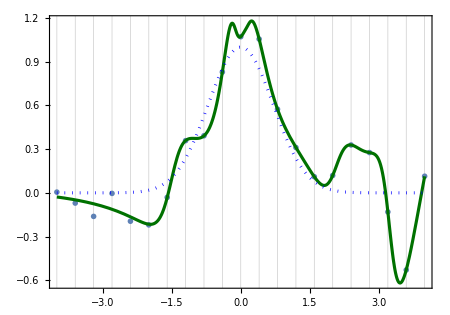
-Graphics-Figure 34. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1/11

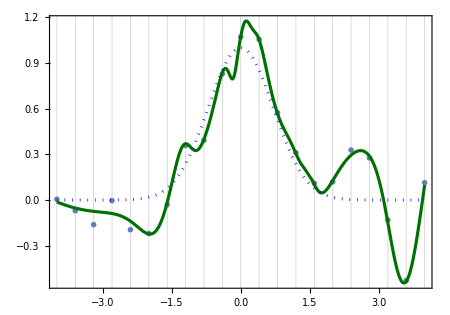
-Graphics-Figure 49. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

1/8

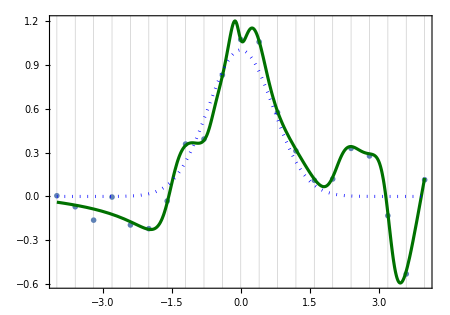
-Graphics-Figure 95. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)